```mathematica
prod1 := k1 s (rT - rp[t])/(kM1+ (rT - rp[t]))
```

```mathematica
deg1 := k2 rp[t]/(kM2+rp[t])
```

```mathematica
par1 = {k1->1, k2->1 , rT-> 1, kM1-> 0.05, kM2->0.05 };
```

```mathematica
sol1 = Solve[prod1 == deg1, rp[t]]
```

{{rp[t]→1/(2 (k2-k1 s))(k2 kM1+k2 rT+k1 kM2 s-k1 rT s+√(-4 k1 kM2 rT s (k2-k1 s)+(-k2 kM1-k2 rT-k1 kM2 s+k1 rT s)^2))},{rp[t]→1/(2 (-k2+k1 s))(-k2 kM1-k2 rT-k1 kM2 s+k1 rT s+√(-4 k1 kM2 rT s (k2-k1 s)+(-k2 kM1-k2 rT-k1 kM2 s+k1 rT s)^2))}}

```mathematica
rp[t] /. sol1 /. par1
```

{(1.05-0.95 s+√((-1.05+0.95 s)^2-0.2 (1-s) s))/(2 (1-s)),(-1.05+0.95 s+√((-1.05+0.95 s)^2-0.2 (1-s) s))/(2 (-1+s))}

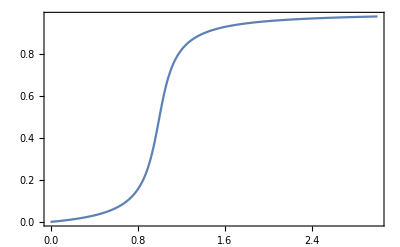

```mathematica
Plot[rp[t] /. sol1[[2]] /. par1,{s,0,3},Frame->True,PlotRange->All]
```

```mathematica
sys1 = D[r[t],t]==k0 + k1 s -k2 r[t]
```

r'[t]==k0+k1 s-k2 r[t]

```mathematica
sys1[[2]]
```

k0+k1 s-k2 r[t]

```mathematica
List@@sys1[[2]]
```

{k0,k1 s,-k2 r[t]}

```mathematica
(List@@sys1[[2]])[[3]][[1]]
```

-1

```mathematica
tmp1 = Cases[List@@sys1[[2]],n1_ /; If[Length[n1]>1, n1[[1]]==-1]]
```

{-k2 r[t]}

```mathematica
Plus@@{a,b,c,d}
```

a+b+c+d

```mathematica
deg1 = Plus@@tmp1
```

-k2 r[t]

```mathematica
Complement[List@@sys1[[2]],tmp1]
```

{k0,k1 s}

```mathematica
prod1 =Plus@@ Complement[List@@sys1[[2]],tmp1]
```

k0+k1 s